# My School’s Energy Consumption Project Notebook

## Managing Permissions

```mathematica
CreatePermissionsGroup["administrator",{$CloudUserID}]
```

```mathematica
SetUsers["administrator",{"admin@myschool.edu","admin2@myschool.edu"}]
```

```mathematica
CreatePermissionsGroup["dataentry",{$CloudUserID}]
```

```mathematica
SetUsers["dataentry",{"dataentry@myschool.edu","dataentry2@myschool.edu"}]
```

```mathematica
CloudShare[EvaluationNotebook[],PermissionsGroup["administrator"]]
```

## Creating Cloud Expressions

## Fuel Oil Deliveries

```mathematica
mySchoolFuelOil=CreateCloudExpression[
Map[{#["DeliveryDate"], #["Gallons"]} &,Normal[SemanticImport["C:\\Users\\kylem\\Documents\\GitHub\\Computational-Sustainability-Toolkit\\Sample Data\\FuelOil_Deliveries.csv"]]],"MySchoolFuelOil"]
```

CloudExpression[…]

```mathematica
DeleteCloudExpression["MySchoolFuelOil"]
```

## Electric Bills

```mathematica
mySchoolElectricBills=CreateCloudExpression[
Map[{#["Bill Date"], #["KWH"]} &,Normal[SemanticImport["C:\\Users\\kylem\\Documents\\GitHub\\Computational-Sustainability-Toolkit\\Sample Data\\Sample_Monthly_Bills.csv"]]],"MySchoolElectriBills"]
```

CloudExpression[…]

```mathematica
DeleteCloudExpression["MySchoolElectriBills"]
```

## Interval Data

```mathematica
mySchoolIntervalData=CreateCloudExpression[
Map[{#["IntervalEnd"], #["Quantity"]} &,Normal[SemanticImport["C:\\Users\\kylem\\Documents\\GitHub\\Computational-Sustainability-Toolkit\\Sample Data\\Sample_Interval_September.csv"]]],"MySchoolIntervalData"]
```

CloudExpression[…]

```mathematica
DeleteCloudExpression["MySchoolIntervalData"]
```

## Forms to Add Data

## Form to add fuel oil deliveries

```mathematica
mySchoolFuelOilForm=FormPage[
{"Date"-><|Interpreter->"Date","Hint"->"Example January 15, 2019"|>,"Gallons"->"Integer"},
AppendTo[CloudExpression["MySchoolFuelOil"],{#Date,#Gallons}]&,
AppearanceRules-><|"Title"->"Enter a fuel oil delivery",
"Description"->"Enter a date and the number of gallons delivered"|>]
```

```mathematica
CloudDeploy[
FormPage[
{"Date"-><|Interpreter->"Date","Hint"->"Example January 15, 2019"|>,"Gallons"->"Integer"},
AppendTo[CloudExpression["MySchoolFuelOil"],{#Date,#Gallons}]&,
AppearanceRules-><|"Title"->"Enter a fuel oil delivery",
"Description"->"Enter a date and the number of gallons delivered"|>],
"MySchoolFuelForm"]
```

CloudObject[https://www.wolframcloud.com/obj/user-58f3ee6b-3083-40a8-9846-527d81df8447/MySchoolFuelForm]

```mathematica
CopyToClipboard[CloudObject["https://www.wolframcloud.com/obj/user-58f3ee6b-3083-40a8-9846-527d81df8447/MySchoolFuelForm"]⟦1⟧]
```

```mathematica
DeleteObject[CloudObject["MySchoolFuelForm"]]
```

DeleteObject::cloudnf: No CloudObject found at the given address

$Failed

```mathematica
SetPermissions[CloudObject["MySchoolFuelForm"],PermissionsGroup["dataentry"]->{"Read","Write","Execute"}]
```

## Form to add Electric Bill

```mathematica
mySchoolElectricBillsForm=FormPage[
{"Date"-><|Interpreter->"Date","Hint"->"Example January 15, 2019"|>,"kWh"->"Integer"},
AppendTo[CloudExpression["MySchoolElectriBills"],{#Date,#kWh}]&,
AppearanceRules-><|"Title"->"Enter monthly kWh consumption",
"Description"->"Enter the date on your bill and the number of kWh delivered"|>]
```

```mathematica
CloudDeploy[FormPage[
{"Date"-><|Interpreter->"Date","Hint"->"Example January 15, 2019"|>,"kWh"->"Integer"},
AppendTo[CloudExpression["MySchoolElectriBills"],{#Date,#kWh}]&,
AppearanceRules-><|"Title"->"Enter monthly kWh consumption",
"Description"->"Enter the date on your bill and the number of kWh delivered"|>],"MySchoolElectricBillsForm"]
```

CloudObject[https://www.wolframcloud.com/obj/user-58f3ee6b-3083-40a8-9846-527d81df8447/MorganElectricBillsForm]

```mathematica
CopyToClipboard[CloudObject["https://www.wolframcloud.com/obj/user-58f3ee6b-3083-40a8-9846-527d81df8447/MySchoolEectricBillsForm"]⟦1⟧]
```

```mathematica
DeleteObject[CloudObject["MySchoolElectricBillsForm"]]
```

```mathematica
SetPermissions[CloudObject["MySchoolElectricBillsForm"],PermissionsGroup["dataentry"]->{"Read","Write","Execute"}]
```

## Function to Add Interval Data

Until a solution is arrived at for adding interval data to cloud expressions through a form, it will have to be managed through code within a notebook.  you could use this function in a shared cloud notebook.

```mathematica
Put[Union[Get[CloudExpression["MySchoolIntervalData"]],
Map[{#["IntervalEnd"], #["Quantity"]} &,
Normal[SemanticImport["C:\\Users\\kylem\\Documents\\GitHub\\Computational-Sustainability-Toolkit\\Sample Data\\Sample_Interval_October.csv"]]]],
CloudExpression["MySchoolIntervalData"]]
```

## Visualizations

## Fuel Oil Visualization

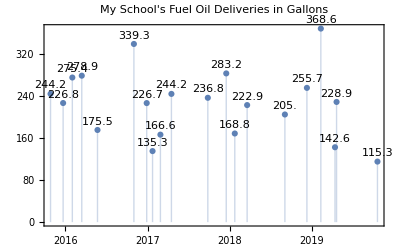

```mathematica
mySchoolFuelOilChart=DateListPlot[TimeSeries[
Get[CloudExpression["MySchoolFuelOil"]]],
Filling->Axis,
Joined->False,
PlotLabel->"My School's Fuel Oil Deliveries in Gallons",
LabelingFunction->(Placed[Last@#1,Above] &),
PlotMarkers->Automatic,
PlotTheme->"Detailed",
ImageSize->Full]
```

```mathematica
CloudDeploy[Delayed[
DateListPlot[TimeSeries[
Get[CloudExpression["MySchoolFuelOil"]]],
Filling->Axis,
Joined->False,
PlotLabel->"My School's Fuel Oil Deliveries in Gallons",
LabelingFunction->(Placed[Last@#1,Above] &),
PlotMarkers->Automatic,
PlotTheme->"Detailed",
ImageSize->Full]],"MySchoolFuelOilChart"]
```

CloudObject[https://www.wolframcloud.com/obj/user-58f3ee6b-3083-40a8-9846-527d81df8447/MySchoolFuelOilChart]

```mathematica
CopyToClipboard[CloudObject["https://www.wolframcloud.com/obj/user-58f3ee6b-3083-40a8-9846-527d81df8447/MySchoolFuelOilChart"]⟦1⟧]
```

```mathematica
DeleteObject[CloudObject["MySchoolFuelOilChart"]]
```

```mathematica
SetPermissions[CloudObject["MySchoolFuelOilChart"],"Public"]
```

{All→Automatic,Owner→{Read,Write,Execute}}

## Electric Bill Visualization

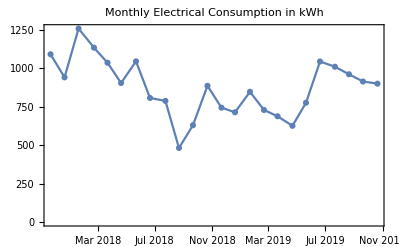

```mathematica
mySchoolElectricBillsChart=DateListPlot[TimeSeries[Get[CloudExpression["MySchoolElectriBills"]]],
PlotLabel->"Monthly Electrical Consumption in kWh",
PlotMarkers->Automatic,
PlotTheme->"Detailed",
ImageSize->Full]
```

```mathematica
CloudDeploy[Delayed[DateListPlot[TimeSeries[Get[CloudExpression["MySchoolElectriBills"]]],
PlotLabel->"Monthly Electrical Consumption in kWh",
PlotMarkers->Automatic,
PlotTheme->"Detailed",
ImageSize->Full]],"MySchoolElectricBillChart"]
```

CloudObject[https://www.wolframcloud.com/obj/user-58f3ee6b-3083-40a8-9846-527d81df8447/MySchoolElectricBillChart]

```mathematica
CopyToClipboard[CloudObject["https://www.wolframcloud.com/obj/user-58f3ee6b-3083-40a8-9846-527d81df8447/MySchoolElectricBillChart"]⟦1⟧]
```

```mathematica
DeleteObject[CloudObject["MySchoolElectricBillChart"]]
```

```mathematica
SetPermissions[CloudObject["MySchoolElectricBillChart"],"Public"]
```

## Interval Data Visualization

```mathematica
morganIntervalDataChart=manipulateDateListPlotTimeSeries[TimeSeries[Get[CloudExpression["MySchoolIntervalData"]]]]
```

```mathematica
CloudDeploy[Delayed[
manipulateDateListPlotTimeSeries[TimeSeries[Get[CloudExpression["MySchoolIntervalData"]]]]],"MySchoolIntervalDataChart"]
```

CloudObject[https://www.wolframcloud.com/obj/user-58f3ee6b-3083-40a8-9846-527d81df8447/MySchoolIntervalDataChart]

```mathematica
CopyToClipboard[CloudObject["https://www.wolframcloud.com/obj/user-58f3ee6b-3083-40a8-9846-527d81df8447/MySchoolIntervalDataChart"]⟦1⟧]
```

```mathematica
DeleteObject[CloudObject["MySchoolIntervalDataChart"]]
```

```mathematica
SetPermissions[CloudObject["MySchoolIntervalDataChart"],"Public"]
```

{All→Automatic,Owner→{Read,Write,Execute}}

## Home Notebook Deployment

```mathematica
CloudDeploy[n32vk_shm17FrontEndObject[LinkObject["n32vk_shm", 3, 1]]17"My School's Energy Consumption Page.nb""C:\\Users\\kylem\\Documents\\GitHub\\Computational-Sustainability-Toolkit\\Code Samples\\My School's Energy Consumption Page.nb","MySchoolNotebook"]
```

CloudObject[https://www.wolframcloud.com/obj/user-58f3ee6b-3083-40a8-9846-527d81df8447/MySchoolNotebook]

```mathematica
DeleteObject[CloudObject["MySchoolNotebook"]]
```

```mathematica
SetPermissions[CloudObject["MySchoolNotebook"],"Public"]
```

{All→Automatic,Owner→{Read,Write,Execute}}